In reality, most of the enzymes in metabolic pathway are product dependent; that is, their rate not only depends on the concentration of the substrate but on the concentration of the product as well.

Here we study some of the risky properties of pathways equiped with enzymes that are not sensitive to their product concentration.

```mathematica
odes={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs={
v1->((V1*s)/K1s)/(1+s/K1s),(* product independent first enzyme *)v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),
v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm={
(* enzyme 1 *)
V1->100,K1s->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
init={
x[0]==1,y[0]==5};
vars={x,y};
```

Check whether all parameters have a value

```mathematica
rateqs/.parm
odes/.rateqs/.parm
```

{v1→250/3,v2→(100 x[t] (1-y[t]/(100 x[t])))/(1+x[t]+y[t]),v3→(100 (1-0.001/y[t]) y[t])/(1.1+y[t])}

{x'[t]==250/3-(100 x[t] (1-y[t]/(100 x[t])))/(1+x[t]+y[t]),y'[t]==-(100 (1-0.001/y[t]) y[t])/(1.1+y[t])+(100 x[t] (1-y[t]/(100 x[t])))/(1+x[t]+y[t])}

The time-dependent solution of the concentrations

```mathematica
tsol=NDSolve[Join[odes/.rateqs/.parm,init],vars,{t,0,100}];
```

A plot of the dynamics of the concentrations

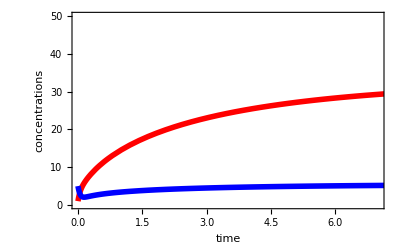

```mathematica
Plot[Evaluate[{x[t],y[t]}/.tsol],{t,0,10},PlotRange->{{0,7},{0,50}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

One should note that the first enzyme is in this model not at all sensitive to what happens further on in the pathway as this can only be communicated to the first enzyme through the concentration of metabolite X.  This means the first enzyme acts as a pump and if functions to fast the second and third enzyme can not catch up and a metabolic explosion occurs.  So if we set the Vmax of the enzyme to a 1000 we obtain this phenomenon (next evaluation cell below). So this is the risk of having a product independent first enzyme.

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

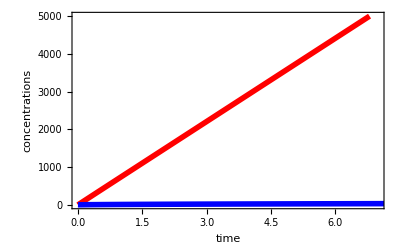

```mathematica
parm2={
(* enzyme 1 *)
V1->1000,K1s->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
tsol2=NDSolve[Join[odes/.rateqs/.parm2,init],vars,{t,0,100}]
Plot[Evaluate[{x[t],y[t]}/.tsol2],{t,0,10},PlotRange->{{0,7},{0,5000}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

We return to the case when the Vmax of the first enzyme is 100 and determine which most the enzyme determines the steady state flux most.

```mathematica
parmchange[param_,newvalue_]:=ReplacePart[parm,Position[parm,param][[1]][[1]]->param->newvalue]
tsolchange[param_,newvalue_]:=NDSolve[Join[odes/.rateqs/.parmchange[param,newvalue],init],vars,{t,0,100}]
sschange[param_,newvalue_]:=FindRoot[Table[odes[[i]][[2]]==0,{i,1, Length[odes]}]/.rateqs/.parmchange[param,newvalue],Table[{vars[[i]][t],(vars[[i]][5]/.tsolchange[param,newvalue])[[1]]},{i,1,Length[vars]}]]
```

We will now calculate the fractional change in the flux divided by a 1% change in the Vmax of the first enzyme, then the 2nd and then the third.  Those coefficients are called flux control coefficients.

```mathematica
CJ1=(((v1/.rateqs/.parmchange[V1,101]/.sschange[V1,101])-(v1/.rateqs/.parmchange[V1,100]/.sschange[V1,100]))/(v1/.rateqs/.parmchange[V1,100]/.sschange[V1,100]))/0.01
CJ2=(((v1/.rateqs/.parmchange[V2,101]/.sschange[V2,101])-(v1/.rateqs/.parmchange[V2,100]/.sschange[V2,100]))/(v1/.rateqs/.parmchange[V2,100]/.sschange[V2,100]))/0.01
CJ3=(((v1/.rateqs/.parmchange[V3,101]/.sschange[V3,101])-(v1/.rateqs/.parmchange[V3,100]/.sschange[V3,100]))/(v1/.rateqs/.parmchange[V3,100]/.sschange[V3,100]))/0.01
```

1.

0

0

So only the first enzyme has a control coefficient larger than 0! Actually it is 1 which means that the 1% change in its maximal activity lead to a 1% change in the steady state flux.  This is not surprising as this is the property of a pump, it sets the rate! When we make the first enzyme product dependent, dependent to x or y, this will change.  This is the situation in realistic metabolic pathways.

Model 2 Competitive inhibition of the first enzyme by metabolite Y.

```mathematica
odes2={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs2={
v1->((V1*s)/K1s)/(1+s/K1s+y[t]/K1y),(* competitive inhibition*)
v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),
v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm2={
(* enzyme 1 *)
V1->100,K1s->1,K1y->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
init2={
x[0]==1,y[0]==5};
vars2={x,y};
```

Check whether all parameters have a value

The time-dependent solution of the concentrations

```mathematica
tsol2=NDSolve[Join[odes2/.rateqs2/.parm2,init2],vars2,{t,0,100}];
```

A plot of the dynamics of the concentrations

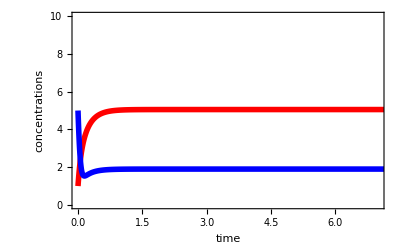

```mathematica
Plot[Evaluate[{x[t],y[t]}/.tsol2],{t,0,10},PlotRange->{{0,7},{0,10}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

A metabolic explosion does not occur now when we increase the Vmax of the first enzyme.  Metabolite X does increase but does not lead to an explosion.

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

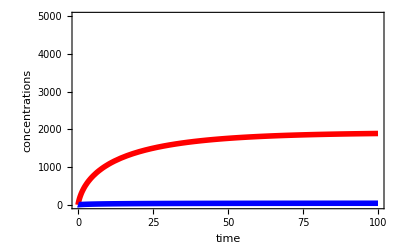

```mathematica
parm3={
(* enzyme 1 *)
V1->1000,K1s->1,K1y->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
tsol3=NDSolve[Join[odes2/.rateqs2/.parm3,init2],vars2,{t,0,100}]
Plot[Evaluate[{x[t],y[t]}/.tsol3],{t,0,100},PlotRange->{{0,100},{0,5000}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

Model 2 Uncompetitive inhibition of the first enzyme by metabolite Y.

```mathematica
odes4={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs4={
v1->((V1*s)/K1s)/((1+s/K1s)(1+y[t]/K1y)),(* competitive inhibition*)
v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),
v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm4={
(* enzyme 1 *)
V1->100,K1s->1,K1y->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
init4={
x[0]==1,y[0]==5};
vars4={x,y};
```

Check whether all parameters have a value

The time-dependent solution of the concentrations

```mathematica
tsol4=NDSolve[Join[odes4/.rateqs4/.parm4,init4],vars4,{t,0,100}];
```

A plot of the dynamics of the concentrations

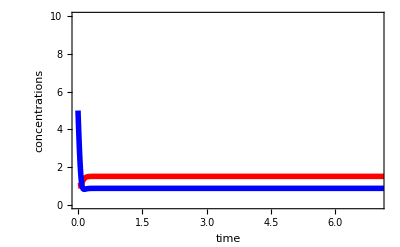

```mathematica
Plot[Evaluate[{x[t],y[t]}/.tsol4],{t,0,10},PlotRange->{{0,7},{0,10}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

A metabolic explosion does not occur now when we increase the Vmax of the first enzyme.  Metabolite X does increase but does not lead to an explosion.

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

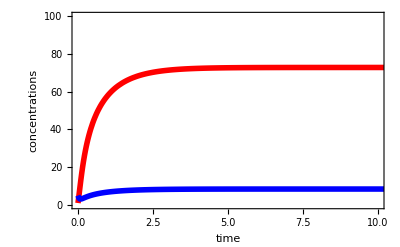

```mathematica
parm5={
(* enzyme 1 *)
V1->1000,K1s->1,K1y->1,
(* enzyme 2 *)
V2->100,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->100,K3y->1,Keq3->100,K3p->1,
(* boundary conditions *)
s->5, p->0.1};
tsol4=NDSolve[Join[odes4/.rateqs4/.parm5,init2],vars2,{t,0,100}]
Plot[Evaluate[{x[t],y[t]}/.tsol4],{t,0,100},PlotRange->{{0,10},{0,100}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"},PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}]
```

Clearly uncompetitive inhibition is much more potent.  X does not increase to ~2000 but only ~70.  This happens because the strength of this inhibition is not depend on the level of X.  Competitive inhibition can be partially overcome by X, but uncompetitive inhibition not.